```mathematica
datapath ="C:\\Users\\Nelson's Laptop\\OneDrive - Universität Zürich UZH\\University\\Master\\LTSpice\\Data\\Same inputs\\";
importdata = Import[#,"Table"]&/@(FileNames[datapath<>"eti_single_layer_hermitian_*.txt"]);
importdata//Dimensions
```

{2,101,3}

```mathematica
importdata[[2,1]]//MatrixForm
```

(Freq.
V(1|1|1|b)
I(R129))

```mathematica
convertedData=Table[Block[{reIm = ToExpression[StringReplace[StringSplit[importdata[[node,i,j]],","],"e"->"*10^"]]},Abs[reIm[[1]]+I*reIm[[2]]]*Exp[I*Arg[reIm[[1]]+I*reIm[[2]]]]],{node,1,Dimensions[importdata][[1]]},{i,2,Dimensions[importdata][[2]]},{j,2,Dimensions[importdata][[3]]}];

impedanceData = Table[(convertedData[[node,i,1]])/(convertedData[[node,i,-1]]),{node,1,Dimensions[convertedData][[1]]},{i,2,Dimensions[convertedData][[2]]}];

freqData = Table[Block[{expr = ToExpression[importdata[[node,i,1]]]},expr],{node,1,Dimensions[importdata][[1]]},{i,2,Dimensions[importdata][[2]]}];
```

```mathematica
convertedData//Dimensions
```

{2,100,2}

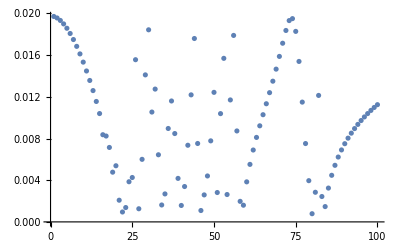

```mathematica
ListPlot[Abs[convertedData[[1,;;,2]]]]
```

```mathematica
Abs[impedanceData]//Dimensions
impedanceData[[1,1]]//MatrixForm
```

{2,99}

0.606435+7.07449 ⅈ

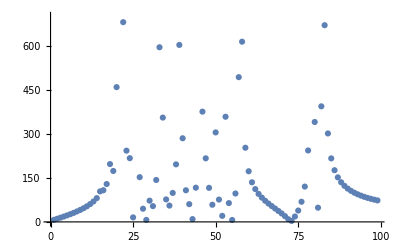

```mathematica
ListPlot[Abs[impedanceData[[1,;;]]]]
```

```mathematica
freqData//Dimensions
```

{2,100}

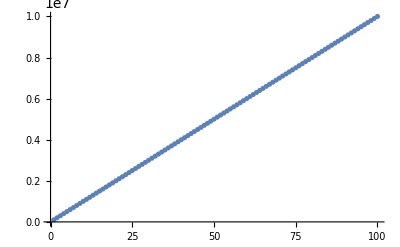

```mathematica
ListPlot[importdata[[2,2;;,1]]]
```

```mathematica
shift = 0;
ticks = Table[{10*i,ToString[i]},{i,1,10}];
tickShift = Table[ticks[[i]]-{shift,0},{i,1,10}];
```

0

```mathematica
impedanceData[[1,1;;]]
```

{0.606435+7.07449 ⅈ,0.614674+10.6834 ⅈ,0.626591+14.3811 ⅈ,0.642606+18.2026 ⅈ,0.663323+22.1875 ⅈ,0.689594+26.383 ⅈ,0.722618+30.846 ⅈ,0.764105+35.6485 ⅈ,0.816561+40.8832 ⅈ,0.883814+46.675 ⅈ,0.972101+53.2004 ⅈ,1.09279+60.7252 ⅈ,1.27179+69.7021 ⅈ,1.61253+81.1642 ⅈ,9.2981+103.789 ⅈ,5.41582+107.978 ⅈ,3.6832+129.266 ⅈ,24.2983+195.938 ⅈ,16.9223+173.121 ⅈ,165.887+429.336 ⅈ,843.985+553.7 ⅈ,586.592-348.287 ⅈ,56.7069-236.559 ⅈ,52.3358-211.248 ⅈ,13.8948+6.74872 ⅈ,702.492-251.338 ⅈ,19.0733-151.573 ⅈ,5.00136-44.7082 ⅈ,3.96434+5.55398 ⅈ,12.5046+71.3599 ⅈ,7.56913+53.3116 ⅈ,10.8618+142.798 ⅈ,215.476+556.136 ⅈ,92.8883-343.91 ⅈ,40.5632+65.1407 ⅈ,18.2618-52.6 ⅈ,16.1704+97.6395 ⅈ,162.532+110.432 ⅈ,341.636+498.584 ⅈ,27.1827-284.336 ⅈ,43.1972-98.9885 ⅈ,5.6314-60.281 ⅈ,6.38833+6.99766 ⅈ,15.0745+115.881 ⅈ,345.838+825.824 ⅈ,47.0671-373.597 ⅈ,18.195-216.363 ⅈ,5.07392-116.196 ⅈ,5.40248-58.3175 ⅈ,299.06+62.9566 ⅈ,9.53341-75.6238 ⅈ,11.3149+17.3126 ⅈ,134.497-332.99 ⅈ,6.75911-63.8654 ⅈ,5.79664+3.08306 ⅈ,12.2544+96.1885 ⅈ,101.757+483.75 ⅈ,88.9271-609.032 ⅈ,10.7841-253.072 ⅈ,4.11887-172.894 ⅈ,2.25919-135.229 ⅈ,1.49141-112.092 ⅈ,1.10643-95.6564 ⅈ,0.892144-82.8339 ⅈ,0.767593-72.1285 ⅈ,0.697003-62.7007 ⅈ,0.663374-54.015 ⅈ,0.658903-45.6819 ⅈ,0.681276-37.3744 ⅈ,0.732531-28.772 ⅈ,0.819565-19.5088 ⅈ,0.956557-9.10642 ⅈ,1.17102+3.13841 ⅈ,1.51891+18.3773 ⅈ,2.12666+38.7294 ⅈ,3.33411+68.7213 ⅈ,6.35825+120.462 ⅈ,18.8661+243.21 ⅈ,440.549+1175.62 ⅈ,47.2611-337.97 ⅈ,19.3377-44.5119 ⅈ,102.088+381.287 ⅈ,92.3443-665.399 ⅈ,11.6352-301.831 ⅈ,4.55766-216.862 ⅈ,2.48946-176.526 ⅈ,1.59165-152.148 ⅈ,1.11523-135.48 ⅈ,0.829732-123.192 ⅈ,0.644117-113.661 ⅈ,0.516164-105.991 ⅈ,0.423979-99.644 ⅈ,0.355228-94.2761 ⅈ,0.302511-89.6554 ⅈ,0.261151-85.6199 ⅈ,0.228075-82.0527 ⅈ,0.201189-78.8669 ⅈ,0.179024-75.9965 ⅈ,0.160528-73.3906 ⅈ}

```mathematica
impedancePlotsAbs = Table[ListLinePlot[Abs[impedanceData[[node,(shift+1);;]]],PlotRange->All,PlotLabel->importdata[[node,1,2]],Ticks->{tickShift,Automatic},AxesLabel->{"Frequenzy","Amplitude"}],{node,1,Dimensions[impedanceData][[1]]}];
```

```mathematica
impedancePlotsAbs//Dimensions
```

{2}

```mathematica
impedancePlotsPhase = Table[ListLinePlot[Arg[impedanceData[[node,(shift+1);;]]],PlotRange->All,PlotLabel->importdata[[node,1,2]],Ticks->{tickShift,Automatic},AxesLabel->{"Frequenzy","Phase"}],{node,1,Dimensions[impedanceData][[1]]}];
```

```mathematica
Manipulate[impedancePlotsAbs[[node]],{node,1,Dimensions[impedanceData][[1]],1}]
```

```mathematica
impedanceData//MatrixForm
```

((1.+1.38778×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+1.38778×10^-17 ⅈ) | (1.-1.38778×10^-17 ⅈ) | (1.-1.38778×10^-17 ⅈ) | (1.-1.38778×10^-17 ⅈ) | (1.+0. ⅈ) | (1.-1.38778×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-1.38778×10^-17 ⅈ) | (1.+1.38778×10^-17 ⅈ) | (1.-1.38778×10^-17 ⅈ) | (1.+1.38778×10^-17 ⅈ) | (1.-1.38778×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+1.38778×10^-17 ⅈ) | (1.-2.77556×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+2.77556×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-2.77556×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-2.77556×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-2.77556×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-2.77556×10^-17 ⅈ) | (1.-2.77556×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-2.77556×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+2.77556×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+2.77556×10^-17 ⅈ) | (1.+2.77556×10^-17 ⅈ) | (1.-2.77556×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+1.11022×10^-16 ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.-2.77556×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.-2.77556×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.-1.38778×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-2.77556×10^-17 ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ)
(1.+0. ⅈ) | (1.-2.77556×10^-17 ⅈ) | (1.-2.77556×10^-17 ⅈ) | (1.+2.77556×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-2.77556×10^-17 ⅈ) | (1.+0. ⅈ) | (1.-2.77556×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+2.77556×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-2.77556×10^-17 ⅈ) | (1.+0. ⅈ) | (1.-2.77556×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+2.77556×10^-17 ⅈ) | (1.-2.77556×10^-17 ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+1.11022×10^-16 ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.-1.11022×10^-16 ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+1.11022×10^-16 ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.-1.11022×10^-16 ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+2.77556×10^-17 ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+1.11022×10^-16 ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.-2.77556×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+2.77556×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.-2.77556×10^-17 ⅈ) | (1.+0. ⅈ) | (1.-5.55112×10^-17 ⅈ) | (1.+5.55112×10^-17 ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ) | (1.+0. ⅈ))

```mathematica
absValImpedance=Abs[impedanceData];
```

```mathematica
Dimensions[absValImpedance]
```

{2,198,1}

```mathematica
freqSpan=71;;162;
```

```mathematica
absValTuples=Table[Transpose[{freqData[[node,freqSpan]],absValImpedance[[node,freqSpan,q]]}],{node,1,Dimensions[absValImpedance][[1]]},{q,1,Dimensions[absValImpedance][[3]]}];
```

```mathematica
absValTuples//Dimensions
```

{2,1,92,2}

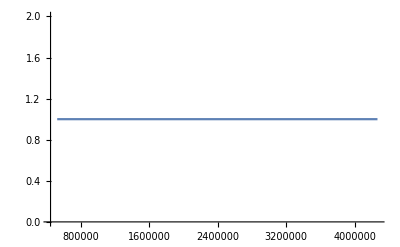

```mathematica
ListPlot[absValTuples[[1,1]],Joined->True,PlotRange->All]
```

```mathematica
Dimensions[absValTuples]
```

{128,92,2}

```mathematica
firstQuadrRange==Join[Range[1,8],Range[17,24],Range[33,40],Range[49,56]];
SubAfirstQuadrRange=Join[Range[1,8],Range[17,24],Range[33,40],Range[49,56]][[1;;All;;2]]
SubBfirstQuadrRange=Join[Range[1,8],Range[17,24],Range[33,40],Range[49,56]][[2;;All;;2]]
```

{1,3,5,7,17,19,21,23,33,35,37,39,49,51,53,55}

{2,4,6,8,18,20,22,24,34,36,38,40,50,52,54,56}

```mathematica
(*First quadrant:*)
subAPlotReady=Transpose[Partition[absValTuples[[SubAfirstQuadrRange]],4]];
subBPlotReady=Transpose[Partition[absValTuples[[SubBfirstQuadrRange]],4]];
```

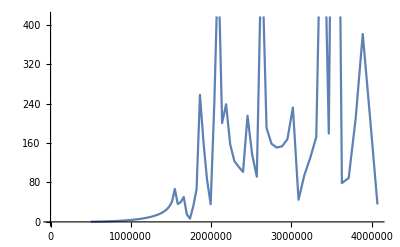

```mathematica
ListPlot[subAPlotReady[[1,1,All]],Joined->True]
```

```mathematica
p1=Flatten[Table[{{5-p,5-q,2},{5-p,5-q,1}},{p,1,4},{q,1,4}],2];
p2=Flatten[Table[{{9-p,5-q,2},{9-p,5-q,1}},{p,1,4},{q,1,4}],2];
p3=Flatten[Table[{{4+p,4+q,1},{4+p,4+q,2}},{p,1,4},{q,1,4}],2];
p4=Flatten[Table[{{p,4+q,1},{p,4+q,2}},{p,1,4},{q,1,4}],2];
correspondingNodeCoords=Join[p1,p2,p3,p4];
```

```mathematica
pathETIWithinGit="D:\\GitHubDesktop\\eti\\";
pathWithMult=pathETIWithinGit<>"Data\\singling_out_device_parts\\obc_single_layer_2022_09_13\\Layer_01\\";
pathByHand=pathETIWithinGit<>"Data\\singling_out_device_parts\\comparison_multiplexer_no_multiplexer\\byHand\\";
```

```mathematica
impWithMult=Import[#,"Table",HeaderLines->2]&/@(FileNames[pathWithMult<>"2D_*.dat"]);
impByHand=Import[#,"Table",HeaderLines->2]&/@(FileNames[pathByHand<>"2D_*.dat"]);
```

```mathematica
nodeCoordAndDataWithMult=Transpose[{p1,impWithMult}];
sortedDataWithMult=Partition[SortBy[nodeCoordAndDataWithMult,#[[1,1]]*1+#[[1,2]]*100+#[[1,3]]*10&],4];
```

```mathematica
Dimensions[impWithMult]
```

{32,513,5}

```mathematica
nodeCoordAndDataByHand=Transpose[{p1,impByHand}];
sortedDataByHand=Partition[SortBy[nodeCoordAndDataByHand,#[[1,1]]*1+#[[1,2]]*100+#[[1,3]]*10&],4];
```

```mathematica
Dimensions[sortedDataWithMult]
```

{8,4,2}

```mathematica
subAExpWithMultplexerPlotReady=sortedDataWithMult[[1;;All;;2,All,2,All,{1,2}]];
subBExpWithMultplexerPlotReady=sortedDataWithMult[[2;;All;;2,All,2,All,{1,2}]];
```

```mathematica
subAByHandExpPlotReady=sortedDataByHand[[1;;All;;2,All,2,All,{1,2}]];
subBByHandExpPlotReady=sortedDataByHand[[2;;All;;2,All,2,All,{1,2}]];
```

```mathematica
subASpan=1;;All;;2;
subBSpan=2;;All;;2;
```

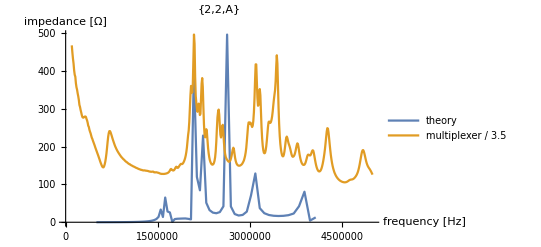

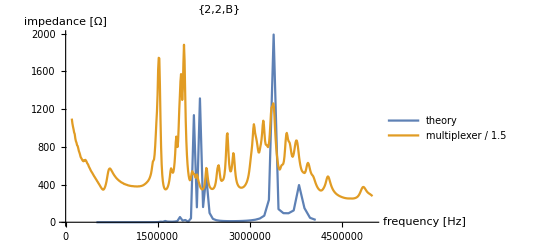

```mathematica
p=2;
q=2;
factorA=3.5;
factorB=1.5;
ListPlot[{subAPlotReady[[p,q,All]],Function[x,{x[[1]], x[[2]]/factorA}]/@subAExpWithMultplexerPlotReady[[p,q,All]]},PlotLabel->If[sortedDataWithMult[[subASpan]][[p,q,1,3]]==1,{sortedDataWithMult[[subASpan]][[p,q,1,1]],sortedDataWithMult[[subASpan]][[p,q,1,2]],"A"},{sortedDataWithMult[[subASpan]][[p,q,1,1]],sortedDataWithMult[[subASpan]][[p,q,1,2]],"B"}],Joined->True,PlotRange->All,PlotLegends->{"theory","multiplexer / "<>ToString[factorA]},AxesLabel->{"frequency [Hz]","impedance [Ω]"}]

ListPlot[{subBPlotReady[[p,q,All]],Function[x,{x[[1]], x[[2]]/factorB}]/@subBExpWithMultplexerPlotReady[[p,q,All]]},PlotLabel->If[sortedDataWithMult[[subBSpan]][[p,q,1,3]]==1,{sortedDataWithMult[[subBSpan]][[p,q,1,1]],sortedDataWithMult[[subBSpan]][[p,q,1,2]],"A"},{sortedDataWithMult[[subBSpan]][[p,q,1,1]],sortedDataWithMult[[subBSpan]][[p,q,1,2]],"B"}],Joined->True,PlotRange->All,PlotLegends->{"theory","multiplexer / "<>ToString[factorB]},AxesLabel->{"frequency [Hz]","impedance [Ω]"}]
```

```mathematica
(*
Do[
pq={{1,1},{1,2},{2,1},{2,2}};
factorAB={{2.5,2.5},{2.5,2.5},{5.,4.5},{3.5,1.5}};
Export["theory_vs_multiplexer_first_quadrant_sublattice_A_node_"<>ToString[If[sortedDataWithMult[[subASpan]][[pq[[elem,1]],pq[[elem,2]],1,3]]==1,{sortedDataWithMult[[subASpan]][[pq[[elem,1]],pq[[elem,2]],1,1]],sortedDataWithMult[[subASpan]][[pq[[elem,1]],pq[[elem,2]],1,2]],"A"},{sortedDataWithMult[[subASpan]][[pq[[elem,1]],pq[[elem,2]],1,1]],sortedDataWithMult[[subASpan]][[pq[[elem,1]],pq[[elem,2]],1,2]],"B"}]]<>".pdf",
ListPlot[{subAPlotReady[[pq[[elem,1]],pq[[elem,2]],All]],Function[x,{x[[1]], x[[2]]/factorAB[[elem,1]]}]/@subAExpWithMultplexerPlotReady[[pq[[elem,1]],pq[[elem,2]],All]]},PlotLabel->If[sortedDataWithMult[[subASpan]][[pq[[elem,1]],pq[[elem,2]],1,3]]==1,{sortedDataWithMult[[subASpan]][[pq[[elem,1]],pq[[elem,2]],1,1]],sortedDataWithMult[[subASpan]][[pq[[elem,1]],pq[[elem,2]],1,2]],"A"},{sortedDataWithMult[[subASpan]][[pq[[elem,1]],pq[[elem,2]],1,1]],sortedDataWithMult[[subASpan]][[pq[[elem,1]],pq[[elem,2]],1,2]],"B"}],Joined->True,PlotRange->All,PlotLegends->{"theory","multiplexer / "<>ToString[factorAB[[elem,1]]]},AxesLabel->{"frequency [MHz]","impedance [Ω]"},Ticks->{Table[{m 10^6,m},{m,0,4,0.5}],Automatic}]];
Export["theory_vs_multiplexer_first_quadrant_sublattice_B_node_"<>ToString[If[sortedDataWithMult[[subBSpan]][[pq[[elem,1]],pq[[elem,2]],1,3]]==1,{sortedDataWithMult[[subBSpan]][[pq[[elem,1]],pq[[elem,2]],1,1]],sortedDataWithMult[[subBSpan]][[pq[[elem,1]],pq[[elem,2]],1,2]],"B"},{sortedDataWithMult[[subBSpan]][[pq[[elem,1]],pq[[elem,2]],1,1]],sortedDataWithMult[[subBSpan]][[pq[[elem,1]],pq[[elem,2]],1,2]],"B"}]]<>".pdf",
ListPlot[{subBPlotReady[[pq[[elem,1]],pq[[elem,2]],All]],Function[x,{x[[1]], x[[2]]/factorAB[[elem,2]]}]/@subBExpWithMultplexerPlotReady[[pq[[elem,1]],pq[[elem,2]],All]]},PlotLabel->If[sortedDataWithMult[[subASpan]][[pq[[elem,1]],pq[[elem,2]],1,3]]==1,{sortedDataWithMult[[subASpan]][[pq[[elem,1]],pq[[elem,2]],1,1]],sortedDataWithMult[[subASpan]][[pq[[elem,1]],pq[[elem,2]],1,2]],"B"},{sortedDataWithMult[[subASpan]][[pq[[elem,1]],pq[[elem,2]],1,1]],sortedDataWithMult[[subASpan]][[pq[[elem,1]],pq[[elem,2]],1,2]],"B"}],Joined->True,PlotRange->All,PlotLegends->{"theory","multiplexer / "<>ToString[factorAB[[elem,2]]]},AxesLabel->{"frequency [MHz]","impedance [Ω]"},Ticks->{Table[{m 10^6,m},{m,0,4,0.5}],Automatic}]]
,{elem,1,4}]
*)
```

```mathematica
(*
Export["theory_vs_multiplexer_first_quadrant_sublattice_A_node_"<>ToString[If[sortedDataWithMult[[subASpan]][[p,q,1,3]]==1,{sortedDataWithMult[[subASpan]][[p,q,1,1]],sortedDataWithMult[[subASpan]][[p,q,1,2]],"A"},{sortedDataWithMult[[subASpan]][[p,q,1,1]],sortedDataWithMult[[subASpan]][[p,q,1,2]],"B"}]]<>".pdf",
ListPlot[{subAPlotReady[[p,q,All]],Function[x,{x[[1]], x[[2]]/factorA}]/@subAExpWithMultplexerPlotReady[[p,q,All]]},PlotLabel->If[sortedDataWithMult[[subASpan]][[p,q,1,3]]==1,{sortedDataWithMult[[subASpan]][[p,q,1,1]],sortedDataWithMult[[subASpan]][[p,q,1,2]],"A"},{sortedDataWithMult[[subASpan]][[p,q,1,1]],sortedDataWithMult[[subASpan]][[p,q,1,2]],"B"}],Joined->True,PlotRange->All,PlotLegends->{"theory","multiplexer / "<>ToString[factorA]},AxesLabel->{"frequency [MHz]","impedance [Ω]"},Ticks->{Table[{m 10^6,m},{m,0,4,0.5}],Automatic}]]
Export["theory_vs_multiplexer_first_quadrant_sublattice_B_node_"<>ToString[If[sortedDataWithMult[[subBSpan]][[p,q,1,3]]==1,{sortedDataWithMult[[subBSpan]][[p,q,1,1]],sortedDataWithMult[[subBSpan]][[p,q,1,2]],"B"},{sortedDataWithMult[[subBSpan]][[p,q,1,1]],sortedDataWithMult[[subBSpan]][[p,q,1,2]],"B"}]]<>".pdf",
ListPlot[{subBPlotReady[[p,q,All]],Function[x,{x[[1]], x[[2]]/factorB}]/@subBExpWithMultplexerPlotReady[[p,q,All]]},PlotLabel->If[sortedDataWithMult[[subASpan]][[p,q,1,3]]==1,{sortedDataWithMult[[subASpan]][[p,q,1,1]],sortedDataWithMult[[subASpan]][[p,q,1,2]],"B"},{sortedDataWithMult[[subASpan]][[p,q,1,1]],sortedDataWithMult[[subASpan]][[p,q,1,2]],"B"}],Joined->True,PlotRange->All,PlotLegends->{"theory","multiplexer / "<>ToString[factorB]},AxesLabel->{"frequency [MHz]","impedance [Ω]"},Ticks->{Table[{m 10^6,m},{m,0,4,0.5}],Automatic}]]
*)
```